```mathematica
AsymptoticIntegrate[√Sinh[x t],{t,0,1},{x,0,1}]
AsymptoticIntegrate[ⅇ^(-x/t),{t,0,1},{x,0,1}]
```

(2 √x)/3

1+x (-1+EulerGamma+Log[x])

```mathematica
∫_0^1 ⅇ^(-x/t)ⅆt
Series[%,{x,0,2}]
```

ConditionalExpression[ⅇ^-x-x Gamma[0,x], Re[x]≥0]

ConditionalExpression[ⅇ^-x-x Gamma[0,x], Re[x]≥0]

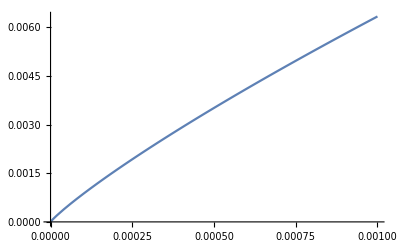

```mathematica
Plot[{Abs[ⅇ^-x-NIntegrate[ⅇ^(-x/t),{t,0,1}]]},{x,0,0.001}]
```

```mathematica
D[ⅇ^(-x/t), t]
```

(ⅇ^(-x/t) x)/t^2

```mathematica
lim_(x->0^+) (∫_0^1 x/t ⅇ^(-x/t)ⅆt)/ⅇ^-x
```

0

```mathematica
Assuming[m<=1,∫_0^(π/2) 1/(√(1-m Cos[θ]^2))ⅆθ//FullSimplify]
Assuming[ϵ>=0,Asymptotic[EllipticK[1-ϵ^2],{ϵ,0,2}]//FullSimplify//Expand]
AsymptoticIntegrate[1/(√(1-m Cos[θ]^2)),{θ,0,π/2},m->1]
```

EllipticK[m]

-ϵ^2/4+Log[4]-1/4 ϵ^2 Log[ϵ/4]-Log[ϵ]

-5/8 Log[-1+m]+1/8 m Log[-1+m]